#### CSE 477 Instructor: Dianne Hansford Homework 2: Exploring Least Squares Approximation with Bezier Curves Due: October 6 (Sunday), 2016 by 11:59pm

The purpose of this homework is to explore least squares approximation with Bezier curves.  
The program flow is as follows.
1) Input data points to be approximated 
2) Uniform or chord length parameters are created for the data.
3) Input the degree n of the approximation
4) Approximate the data with a degree n Bezier curve
    This program finds the approximation with both sets of parameter values so they may be displayed together.
5) Measure error between the Bezier curve and the input data.
6) Display the input, approximation, errors
7) Document your observations. 
Details for each of these steps are given below in the blue sections. You must complete the code when instructed to do so. I have supplied some code and graphics for you.
See the Observations section for instructions for the final report: running the data sets and reporting.
Instructions on how to get started will be given in class.

Guidelines:
Turn in via Canvas
Name your file lastname_HW2.nb
Remove output from your file before uploading (Cell -- > Delete All Output)
Below each problem description, add your MM code
Comment your notebook
Work independently

Grading: 100 pts total
Here are the elements that will be graded
Uniform parameters 5
Chord length parameters 10
Least squares approximation  25
Error calculation 10
Observations  50

Bezier Curve Evaluator
(You do not need to change this routine.)

```mathematica
curve[bpts_,deg_,t_]:=Sum[BernsteinBasis[deg,i,t]*bpts[[i+1]],{i,0,deg}];
```

Data Sets
Below are some sample data sets
Create numdata =  number of data to be approximated
Create data (x,y) or (x,y,z) points to be approximated
Load one data set into “data”

```mathematica
(* uniformly sampled line *)
bpts = {{0,0}, {1,1}, {2,2},{3,3}};
dataUniformline = Table[curve[bpts, Length[bpts]-1, t],{t,0,1, 1.0/10.0}];

(* Noisy line *)
dataNoisyLine = Table[{t,t + 0.2*RandomReal[]},{t,0,1, 1.0/30.0}];

(* nice curve: classic car fender sillouette *)
bpts = {{0,0}, {0,1}, {0,2},{20,3}};
dataGF = Table[curve[bpts, Length[bpts]-1, t],{t,0,1, 1.0/20.0}];

(* This data set has a gap in the data -- suppose some part was occluded or data lost *)
dataGFgap = {{0,0},{0.0025000000000000005,0.15000000000000002},{0.020000000000000004,0.30000000000000004},{0.06750000000000003,0.45000000000000007},{0.16000000000000003,0.6000000000000002},{0.3125,0.75},{0.5400000000000003,0.9000000000000001},{0.8575000000000002,1.05},{1.2800000000000002,1.2000000000000002},{1.8225000000000002,1.3500000000000003},{5.4925000000000015,1.95},{6.860000000000001,2.1},{8.4375,2.25},{10.240000000000002,2.4000000000000004},{12.282500000000002,2.5500000000000003},{14.580000000000002,2.7},{17.1475,2.8499999999999996},{20,3}};


(* four points *)
bpts = {{0,0}, {0.0, 1.0}, {2.0, 1.0},{2.0, 0.0}};
dataFour = Table[curve[bpts, Length[bpts]-1, t],{t,0,1, 1.0/3.0}];


(* This is a data set to simulate an outlier *)
dataOutlier = Table[{t,Sin[t]},{t,0,Pi, 1.0/10.0}];
dataOutlier[[17,2]] = dataOutlier[[17,2]] - 0.5;

(* semicircle *)
dataSemiCircle = Table[{Cos[t],Sin[t]//N},{t,0,Pi, Pi/10.0}];

(* spiral  with noise *)
dataSpiral = Table[{t*Cos[t]+0.2*RandomReal[],t*Sin[t]+0.2*RandomReal[]},{t,0,6, 0.2}];

(* spiral reverse *)
dataSpiralRev = Table[{(6-t)*Cos[(6-t)]+0.2*RandomReal[],(6-t)*Sin[(6-t)]+0.2*RandomReal[]},{t,0,6, 0.2}];

(* Selected dataset is dataGF*)
data = dataSpiralRev;
numdata = Length[data];

Print["Input numdata =",numdata];
Print["Data = ",MatrixForm[data]];
```

Uniform parameter values
Input:
numdata: number of data
params: parameter values data structure
Output: 
params: uniform parameter values associated with each data 
Note: params[[1]] = 0.0 and params[[numdata]] = 1.0

You must write this routine

```mathematica
uniformparams[numdata_] :=(
n= numdata-1;
 Do[
params[[i+1]]=(i/(n)),
{i,0,n}];
Print["Uniform parameters = ",params//N]; 
);
```

Chord length parameters
Input: 
data (x,y) or (x,y,z) points 
numdata: number of data 
params: parameter values data structure
Output: 
params: chord length parameter values associated with each data
Note: params[[1]] = 0.0 and params[[numdata]] = 1.0

You must write this routine.

```mathematica
chordlengthparams[data_, numdata_] :=(
n= numdata-1;
distPoint=Sum[EuclideanDistance[data[[i]], data[[i+1]]],{i,1,n}];
 Do[
params[[i+1]]=Sum[EuclideanDistance[data[[j]], data[[j+1]]],{j,1,i}]/distPoint,{i,1,n}];
Print["chordlength parameters = ",params//N];
);
```

Least squares approximation with Bezier curve
Input: 
n: degree of approximation (3)
data: (x,y) or (x,y,z) points to approximate
numdata: number of data points (l+1)
params: parameter value for each data point (params[[i]])
Output:
Bezier points bez
Note:
You must set up the normal equations yourself, but you can use LinearSolve to solve the normal equations.
Matrix multiplication in MM is with a “.”: mat1.mat2

You must write this routine.

```mathematica
approx[n_, params_, data_]:=(
mat = Table[1.0*BernsteinBasis[n, j-1,params[[i]]], {i,numdata}, {j,6}];
matT = Transpose[mat];
matNew = matT.mat;
matPar = matT.data;
bez = LinearSolve[matNew,matPar];
Print[" solution = ",MatrixForm[bez],"  Bezier points"];
);
```

Least squares error reporting
Input:
data: data points
numdata: number of data points
params: parameters assigned to each data
bez: bezier curve approximating data
deg: degree of Bezier curve
Return as a vector
 {total error, average error, min error, and max error}
 
 You must write this routine.

```mathematica
lsqerror[data_, numdata_, params_, bez_, deg_] :=(
these = Table[curve[bez,deg,params[[i]]],{i,1, numdata}];

sum = Sum[EuclideanDistance[data[[i]], these[[i]]], {i, numdata}];
minerror = Min[Table[EuclideanDistance[data[[i]], these[[i]]],{i,numdata}]];
maxerror = Max[Table[EuclideanDistance[data[[i]], these[[i]]],{i,numdata}]];
aveerror = Mean[Table[EuclideanDistance[data[[i]], these[[i]]],{i,numdata}]];

errors = {sum, aveerror, minerror, maxerror};
Return[errors];
);
```

Establish minmax box for control points and data points
This mmbox is used for the display of the uniform and chord lgth curves, so they are displayed at the same scale.
Input:
bez, deg : Bezier curve and degree
data, numdata : data points and number of them
Output:
plotmm holding {min corner, max corner}

No changes to this routine.

```mathematica
setMinMax[bez_, deg_, data_, numdata_] :=(
(* data structure to hold mmbox *)
plotmm = {{0,0},{0,0}};
(* work on x coordinate *)

bezmin = Min/@Transpose[bez];
bezmax = Max/@Transpose[bez];

datamin = Min/@Transpose[data];
datamax = Max/@Transpose[data];

plotmm[[1,1]] = Min[bezmin[[1]], datamin[[1]]];
plotmm[[1,2]] = Min[bezmin[[2]], datamin[[2]]];

plotmm[[2,1]] = Max[bezmax[[1]], datamax[[1]]];
plotmm[[2,2]] = Max[bezmax[[2]], datamax[[2]]];

(* make the mmbox a little bigger taht the data *)
pbigger = 0.05;
deltax = plotmm[[2,1]] - plotmm[[1,1]];
deltay = plotmm[[2,2]] - plotmm[[1,2]];
offx = deltax*pbigger;
offy = deltay*pbigger;
plotmm[[1,1]] = plotmm[[1,1]] - offx;
plotmm[[1,2]] = plotmm[[1,2]] - offy;
plotmm[[2,1]] = plotmm[[2,1]] + offx;
plotmm[[2,2]] = plotmm[[2,2]] + offy;

(* Print["plotmm = ",plotmm]; *)
);
```

Create graphics entities
data points, Bezier control points, Bezier control polygon, Bezier curve

No changes to this routine.

```mathematica
createGraphics[deg_] :=(
(* Create graphics entities for input data *)
dplot=ListPlot[data, PlotStyle->{Black,PointSize[Medium]}];
(* Graphics entity for Bezier points and Bezier curve *)
points=Graphics[{RGBColor[0.5,0.79,0.81],PointSize[Large],Point[bez]}];
bplot=ListLinePlot[bez,PlotStyle->RGBColor[0.5,0.79,0.81]];
cplot = Graphics[{Thick, Blue,BezierCurve[bez, SplineDegree->deg]}];
);
```

“Main” routine
Create the approximating Bezier curve based on the input knot selection method

Here you set the degree as described in the observations section.

```mathematica
(* Choose degree of approximation *)
approxdeg = 5;

(* Create data structure for paramters *)
params = Table[0,{i,1,numdata}];


(* Create the approximate with uniform parameters *)
uniformparams[numdata];
approx[approxdeg, params, data];
uniformErrors =lsqerror[data, numdata, params, bez, approxdeg];
(* find the minmax of the control points and data points for plotting *)
setMinMax[bez, approxdeg, data, numdata];
createGraphics[approxdeg];
uniformgraphics = Show[{cplot,points,bplot,dplot}, Axes->False, PlotRange->{{plotmm[[1,1]],plotmm[[2,1]]},{plotmm[[1,2]],plotmm[[2,2]]}}];


(* Create the approximate with chordlength parameter *)
chordlengthparams[data, numdata];
approx[approxdeg, params, data];
chordErrors =lsqerror[data, numdata, params, bez, approxdeg];
createGraphics[approxdeg];
chordgraphics = Show[{cplot,points,bplot,dplot},Axes->False, PlotRange->{{plotmm[[1,1]],plotmm[[2,1]]},{plotmm[[1,2]],plotmm[[2,2]]}}];


(* Display results *)

(* number of digits to report error *)
ndigit = 3;
Print["  "];
Print[Style["RESULTS: ", FontSize->15,FontWeight->Bold]]; 
Print[Style["Each approximate is degree = ",FontSize->15], Style[approxdeg,FontSize->15]];
Print[Style["                 Errors ",FontSize->15]];
 
(* Load stats for table display *)
results = Table[If[i==0, {numdata, numdata},{ScientificForm[uniformErrors[[i]],ndigit],ScientificForm[chordErrors[[i]],ndigit]}],{i,0,4}];
 
TableForm[results,TableDirections->Row,TableHeadings->{{"# Data  ","Total  ", "Ave       ", "Min       ", "Max  "},{"Uniform","Chord lgth"}}]

Print[Style["Left: uniform parametrization        Right: chord length parametrization", FontSize->15]];


GraphicsRow[{uniformgraphics, chordgraphics}]
```

Observations
Run each of the data sets that I have supplied for degree 5.
-- Select the parameters inputs, results, and graphics cells and merge the cells.
-- Cut and paste the resulting cell below.
-- Add the data set name at the top of the cell pasted below.
(I have put an example below -- delete it and replace it with your own.)

Examine the graphics display and errors for the approximations. 
For each data set, just below the output, comment on the behavior of the approximation based on the degree and parameters. Anything interesting/special?
Share any general observations you have regarding the two parameter generation methods and the approximation degree.
Your observations must be formatted text.

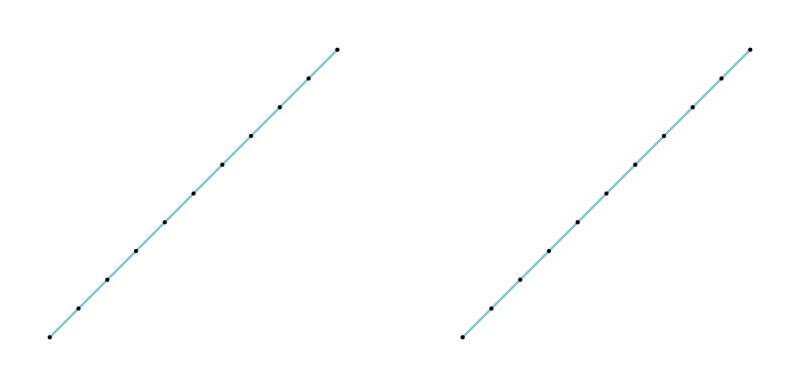
dataUniformLine
"Uniform parameters = "{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}
" solution = "(-9.3327×10^-16 | -9.3327×10^-16
0.6 | 0.6
1.2 | 1.2
1.8 | 1.8
2.4 | 2.4
3. | 3.)"  Bezier points"
"chordlength parameters = "{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}
" solution = "(-8.00247×10^-17 | -8.00247×10^-17
0.6 | 0.6
1.2 | 1.2
1.8 | 1.8
2.4 | 2.4
3. | 3.)"  Bezier points"
"  "
"RESULTS: "
"Each approximate is degree = "5
"                 Errors "
 | "# Data  " | "Total  " | "Ave       " | "Min       " | "Max  "
"Uniform" | 11 | "1.31"×10^("-14") | "1.19"×10^("-15") | "6.28"×10^("-16") | "2.2"×10^("-15")
"Chord lgth" | 11 | "3.88"×10^("-15") | "3.53"×10^("-16") | "0." | "6.28"×10^("-16")
"Left: uniform parametrization        Right: chord length parametrization"
-Graphics-
The Uniform Parameters  and Chord Length parameters both produce the same parameters because the data is the same and the data itself is uniform. Uniform parameters has higher total error, average and maximum values compared to the chord length method and this is because the chord length method is generally more accurate because it reflects geometry of points. However, in this case, the nature of the data does not cause any significant difference in the curves that are obtained.

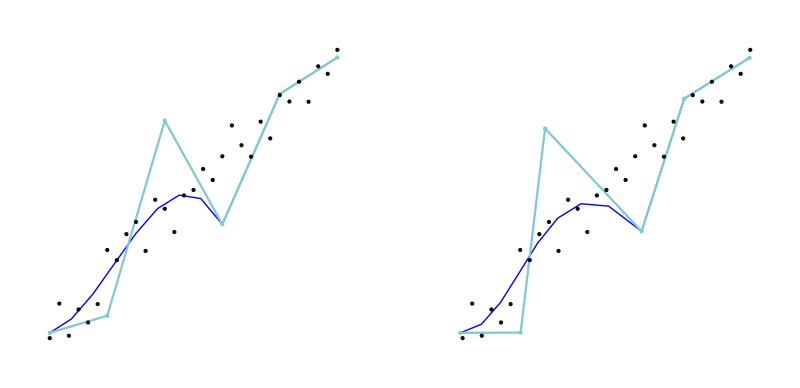
Uniform parameters = {0.,0.0333333,0.0666667,0.1,0.133333,0.166667,0.2,0.233333,0.266667,0.3,0.333333,0.366667,0.4,0.433333,0.466667,0.5,0.533333,0.566667,0.6,0.633333,0.666667,0.7,0.733333,0.766667,0.8,0.833333,0.866667,0.9,0.933333,0.966667,1.}
chordlength parameters = {0.,0.0460336,0.0891218,0.125049,0.14581,0.172439,0.243014,0.260967,0.296555,0.316485,0.35568,0.422509,0.439412,0.471653,0.520161,0.534327,0.563942,0.582626,0.615357,0.656876,0.685119,0.704306,0.750942,0.775705,0.832604,0.847398,0.875631,0.904096,0.951212,0.966849,1.}
RESULTS: 
Each approximate is degree = 5
                 Errors 
 | # Data   | Total   | Ave        | Min        | Max  
Uniform | 31 | 1.39 | 4.47×10^-2 | 4.2×10^-4 | 1.11×10^-1
Chord lgth | 31 | 1.34 | 4.31×10^-2 | 2.82×10^-3 | 1.15×10^-1
Left: uniform parametrization        Right: chord length parametrization
-Graphics-
The chord length parameters and uniform parameters are different due to the way the data is scattered on the plane. Chord length recognizes the distance between the points and calculates the parameters based on that hence the curve on the right would be more accurate. However, the graphs do not show great differences because they are produced from the same data and hence would generally be of the same nature regardless of method of approximation. The control polygons also look similar and in both curves, the highest point and lowest points are not part of the polygon, nor of the curve.
The total, average and maximum errors for the uniform method are higher than those of the chord length method, but the minimum error where the chord length method is higher.

```mathematica
dataNoisyLine
```

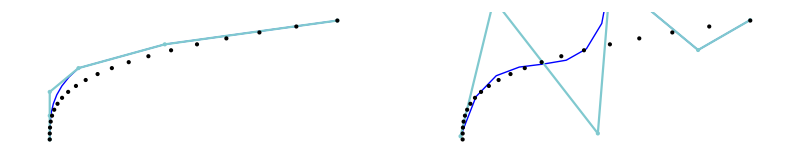
Uniform parameters = {0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}
chordlength parameters = {0.,0.00722928,0.0145066,0.0220886,0.0305808,0.0408886,0.05402,0.0709414,0.0925461,0.119669,0.153108,0.193633,0.242004,0.298965,0.365258,0.441618,0.528778,0.627469,0.738417,0.862352,1.}
Each approximate is degree = 5
                 Errors 
 | # Data   | Total   | Ave        | Min        | Max  
Uniform | 21 | 3.04×10^-14 | 1.45×10^-15 | 5.55×10^-17 | 3.58×10^-15
Chord lgth | 21 | 1.35 | 6.45×10^-2 | 1.3×10^-2 | 1.67×10^-1
Left: uniform parametrization        Right: chord length parametrization
-Graphics-
For this data set, the chord length errors are all higher than the uniform parameters errors. The graphs also show that the uniform parameters better represent a fit to the data. The chord length method, in this case yields hgher errors and a less fitting control polygon.

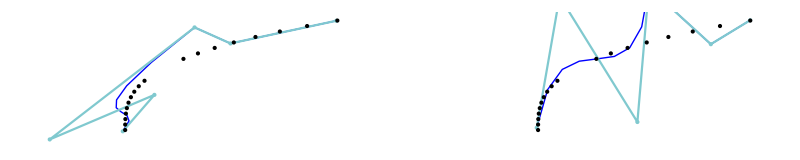
dataGFgap

Uniform parameters = {0.,0.0588235,0.117647,0.176471,0.235294,0.294118,0.352941,0.411765,0.470588,0.529412,0.588235,0.647059,0.705882,0.764706,0.823529,0.882353,0.941176,1.}
chordlength parameters = {0.,0.00722998,0.014508,0.0220907,0.0305837,0.0408926,0.0540252,0.0709482,0.092555,0.119681,0.298898,0.365197,0.441565,0.528733,0.627433,0.738392,0.862339,1.}
RESULTS: 
Each approximate is degree = 5
                 Errors 
 | # Data   | Total   | Ave        | Min        | Max  
Uniform | 18 | 5.61 | 3.12×10^-1 | 1.36×10^-2 | 1.28
Chord lgth | 18 | 1.06 | 5.88×10^-2 | 1.23×10^-2 | 1.43×10^-1
Left: uniform parametrization        Right: chord length parametrization
-Graphics-
There is a very large difference in the errors between Uniform and Chord length data, where chord length has a lower error output as compared to chord length. This is dataGF with gaps and the gaps have caused a massive change in the errors produced by each method of approximation. However, the uniform parameter method's curve still passes through most of the points in the data. The control points of the polygon for the chord length have greater variance than those for uniform parameters.

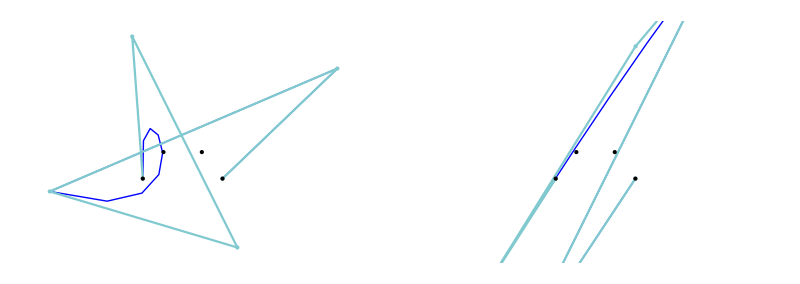
dataFour

Uniform parameters = {0.,0.333333,0.666667,1.}
chordlength parameters = {0.,0.318454,0.681546,1.}
RESULTS: 
                 Errors 
 | # Data   | Total   | Ave        | Min        | Max  
Uniform | 4 | 1.43×10^-16 | 3.58×10^-17 | 0. | 1.11×10^-16
Chord lgth | 4 | 1.05×10^-15 | 2.62×10^-16 | 4.16×10^-17 | 4.45×10^-16
Left: uniform parametrization        Right: chord length parametrization
-Graphics-
The errors are higher for chord length except for Min where chord length error is lower than the uniform parameter error. The resulting curves from both methods are different. Given that the chord length method is more accurate we can conclude the curve shape should be like the one on the right. Since degree and parameters determine curve, the degree of approximation on a few data points should not be too high when dealing with uniform parameters i.e. degree 5 on 4 points. The right curve seems to be interpolating to a polygon that is exactly shaped like itself.

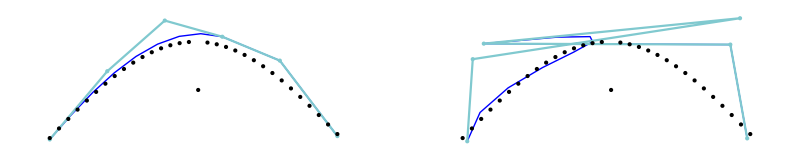
dataOutlier


Uniform parameters = {0.,0.0322581,0.0645161,0.0967742,0.129032,0.16129,0.193548,0.225806,0.258065,0.290323,0.322581,0.354839,0.387097,0.419355,0.451613,0.483871,0.516129,0.548387,0.580645,0.612903,0.645161,0.677419,0.709677,0.741935,0.774194,0.806452,0.83871,0.870968,0.903226,0.935484,0.967742,1.}
chordlength parameters = {0.,0.030916,0.0616782,0.0921367,0.122149,0.151586,0.180331,0.208292,0.235399,0.26161,0.286919,0.311355,0.334988,0.357928,0.380325,0.402362,0.513479,0.623344,0.645568,0.668262,0.691591,0.715682,0.740622,0.766457,0.793194,0.820806,0.849236,0.878398,0.908186,0.938476,0.969129,1.}
RESULTS: 
Each approximate is degree = 5
                 Errors 
 | # Data   | Total   | Ave        | Min        | Max  
Uniform | 32 | 1.13 | 3.55×10^-2 | 2.29×10^-4 | 4.44×10^-1
Chord lgth | 32 | 2.18 | 6.82×10^-2 | 1.76×10^-2 | 4.74×10^-1
Left: uniform parametrization        Right: chord length parametrization
-Graphics-
for this dataset the parameters are not that different on visual inspection. However, the uniform parameters yield lower error values that the chord length parameters. This could be due to the sensitivity of the chord length parameters to point geometry as compared to uniform length parameters. The left polygon and curve look more of a fit than the right ones, and the right curve is distorted at the ends. For this dataset, degree 5 approximation fits well with uniform parameters. The oulier value causes the variances in chord length parameters to increase and hence affects the curve.

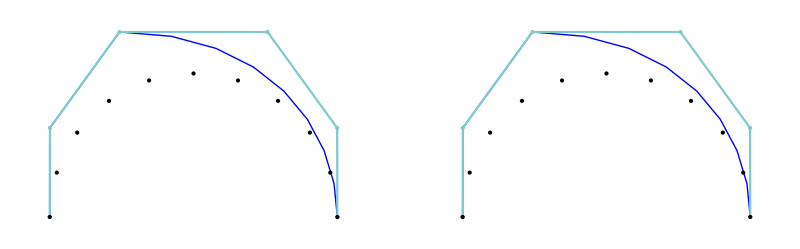
dataSemiCircle

Uniform parameters = {0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}
chordlength parameters = {0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}
RESULTS: 
Each approximate is degree = 5
                 Errors 
 | # Data   | Total   | Ave        | Min        | Max  
Uniform | 11 | 4.32×10^-3 | 3.92×10^-4 | 1.69×10^-4 | 6.42×10^-4
Chord lgth | 11 | 4.32×10^-3 | 3.92×10^-4 | 1.69×10^-4 | 6.42×10^-4
Left: uniform parametrization        Right: chord length parametrization
-Graphics-
Both data methods (uniform and chord length) produce similar curves, control polygons, parameter and error values at 5 degrees of approximation. This could be because of the rules that generated the points which made them uniform ensuring that even whilst using chord length, the values would still be uniform as the geometry is consistent.

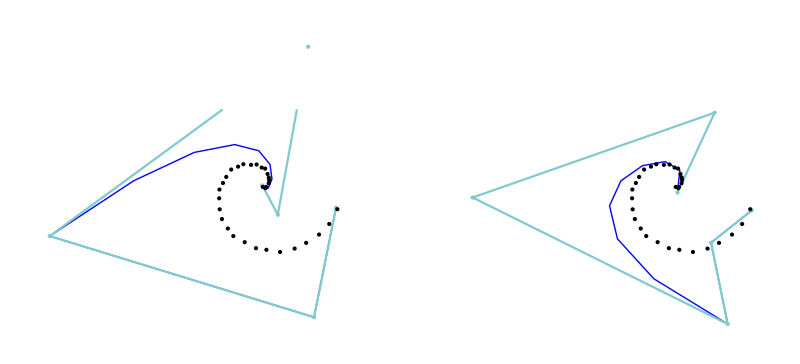
Spiral data


Uniform parameters = {0.,0.0333333,0.0666667,0.1,0.133333,0.166667,0.2,0.233333,0.266667,0.3,0.333333,0.366667,0.4,0.433333,0.466667,0.5,0.533333,0.566667,0.6,0.633333,0.666667,0.7,0.733333,0.766667,0.8,0.833333,0.866667,0.9,0.933333,0.966667,1.}
chordlength parameters = {0.,0.0112609,0.0167285,0.033993,0.0465249,0.056489,0.0709834,0.0937206,0.107661,0.13062,0.152195,0.181984,0.204313,0.233338,0.267688,0.294459,0.323052,0.356953,0.399773,0.438371,0.481401,0.517581,0.56753,0.616782,0.657713,0.711066,0.768977,0.818709,0.878051,0.934888,1.}
RESULTS: 
Each approximate is degree = 5
                 Errors 
 | # Data   | Total   | Ave        | Min        | Max  
Uniform | 31 | 3.22 | 1.04×10^-1 | 1.51×10^-2 | 1.81×10^-1
Chord lgth | 31 | 4.29 | 1.38×10^-1 | 1.58×10^-2 | 4.44×10^-1
Left: uniform parametrization        Right: chord length parametrization
-Graphics-
The uniform parameters yield lower error values that the chord length parameters.  The left polygon and curve look more of a fit than the right ones, and the right curve is distorted at the ends. For this dataset, degree 5 approximation fits well with uniform parameters, though the polygon looks like it has an outlier value.

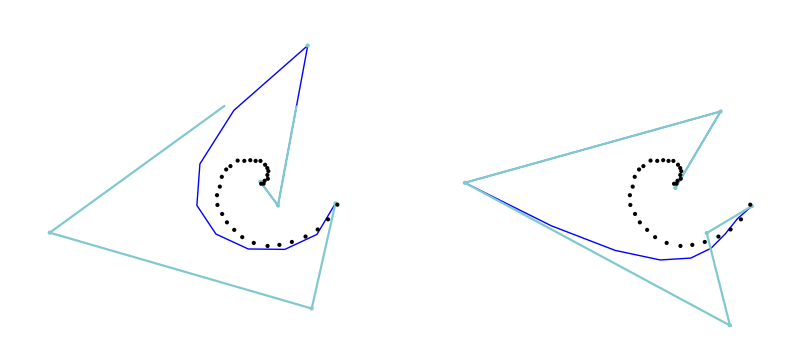
dataSpiralRev


Uniform parameters = {0.,0.0333333,0.0666667,0.1,0.133333,0.166667,0.2,0.233333,0.266667,0.3,0.333333,0.366667,0.4,0.433333,0.466667,0.5,0.533333,0.566667,0.6,0.633333,0.666667,0.7,0.733333,0.766667,0.8,0.833333,0.866667,0.9,0.933333,0.966667,1.}
chordlength parameters = {0.,0.0671997,0.123257,0.177632,0.234457,0.283985,0.329907,0.384522,0.434418,0.476237,0.516749,0.554127,0.593547,0.631351,0.66621,0.704873,0.737937,0.759059,0.794085,0.819876,0.84311,0.863905,0.882733,0.905993,0.921417,0.933953,0.949282,0.964079,0.978892,0.990539,1.}
RESULTS: 
Each approximate is degree = 5
                 Errors 
 | # Data   | Total   | Ave        | Min        | Max  
Uniform | 31 | 3.78 | 1.22×10^-1 | 2.56×10^-2 | 2.3×10^-1
Chord lgth | 31 | 4.38 | 1.41×10^-1 | 9.12×10^-3 | 3.36×10^-1
Left: uniform parametrization        Right: chord length parametrization
-Graphics-
Chord length minimum error values are lower than those of uniform parameters. The right curve looks much more dissociated from its polygon. The data seems to mostly fall outside the curve.

```mathematica
dataGF
```